In the present notebook we examine the  inflationary viability of a scalar field minimally coupled to a rescaled Einstein-Hilbert Gravity, aR. First, we define the potential of the scalar field as function of the inflaton, in thisa power-law model, the so-called chaotic  inflation potential. As it can be shown, this model does not produce a viable phenomenology in the case of aR gravity, yet it does become viable in the context of a quantum corrected R^2 gravity . We calculate the slow-roll indices for this potential using the expressions we have derived from the Friedmann equations for this specific type of modified gravity. Then, we solve the equation ϵ1=1 with respect to ϕ, to obtain its value at the end of inflation and use it in the expression of the e-folding number to find the initial value of ϕ. Moving on, we calculate the slow-roll indiced and observational parameters, that is the spectral index of scalar perturbations and the tensor to scalar ratio, as functions of the model’s free parameters and the e-folding number. We set  N=60 e-foldings and search for which values of the free parameters the Planck 2018 constraints on the spectral index and tensor to scalar ratio can be satisfied, while the slow-roll inflation approximations hold true as well.

```mathematica
The potential under examination is:
```

```mathematica
V[ϕ_]:=λ ϕ/(k^3)
```

```mathematica
The slow-roll indices are:
```

```mathematica
ϵ=1/(2k^2) (V'[ϕ]/V[ϕ])^2
```

1/(2 k^2 ϕ^2)

```mathematica
η=(V''[ϕ]/V[ϕ])/(k^2)
```

0

```mathematica
ϵ1=α ϵ
```

α/(2 k^2 ϕ^2)

```mathematica
ϵ2=-α η +ϵ1
```

α/(2 k^2 ϕ^2)

```mathematica
η=1/k^2 (V''[ϕ]/V[ϕ]) //Simplify
```

0

```mathematica
ϵ1=α ϵ
```

α/(2 k^2 ϕ^2)

```mathematica
ϵ2=-α η +ϵ1 //Simplify
```

α/(2 k^2 ϕ^2)

```mathematica
The expressions of ϕf and ϕi are:
```

```mathematica
Solve[ϵ1==1,ϕ]
```

{{ϕ→-(√α)/(√2 k)},{ϕ→(√α)/(√2 k)}}

```mathematica
ϕf=-(√α)/(√2 k)
```

-(√α)/(√2 k)

```mathematica
Integrate[-k^2/α (V[ϕ]/ V'[ϕ]),ϕ]//Expand
```

-(k^2 ϕ^2)/(2 α)

```mathematica
Solve[Y==-(k^2 ϕf^2)/(2 α)+(k^2 ϕ^2)/(2 α), ϕ]
```

{{ϕ→-(ⅈ √(-1-4 Y) √α)/(√2 k)},{ϕ→(ⅈ √(-1-4 Y) √α)/(√2 k)}}

```mathematica
ϕi=(√(1+4 Y) √α)/(√2 k)
```

(√(1+4 Y) √α)/(√2 k)

```mathematica
The expressions of the slow-roll and observational indices for ϕ=ϕi, i.e at the beginning of inflation, are:
```

The first potential slow-roll parameter:

```mathematica
ϵi=ϵ/.ϕ-> ϕi
```

1/((1+4 Y) α)

```mathematica
Series[1/((1+4 Y) α),{Y,Infinity,2}]
```

1/(4 α Y)-1/(16 α Y^2)+O[1/Y]^3

```mathematica
ϵi=1/(4 α Y)-1/(16 α Y^2)
```

-1/(16 Y^2 α)+1/(4 Y α)

The second potential slow-roll parameter:

```mathematica
ηi=η/.ϕ-> ϕi
```

0

The first Hubble slow-roll parameter:

```mathematica
ϵ1i=ϵ1/.ϕ-> ϕi
```

1/(1+4 Y)

```mathematica
Series[1/(1+4 Y),{Y,Infinity,2}]
```

1/(4 Y)-1/(16 Y^2)+O[1/Y]^3

```mathematica
ϵ1i=1/(4 Y)-1/(16 Y^2)
```

-1/(16 Y^2)+1/(4 Y)

The second Hubble slow-roll parameter:

```mathematica
ϵ2i=ϵ2/. ϕ-> ϕi
```

1/(1+4 Y)

```mathematica
Series[ϵ2i,{Y,Infinity,2}]
```

1/(4 Y)-1/(16 Y^2)+O[1/Y]^3

```mathematica
ϵ2i=1/(4 Y)-1/(16 Y^2)
```

-1/(16 Y^2)+1/(4 Y)

The spectral index of scalar perturbations:

```mathematica
ns=1-6α ϵi+2α ηi //Expand
```

1+3/(8 Y^2)-3/(2 Y)

The tensor to scalar ratio:

```mathematica
r=16α ϵi //Simplify
```

(-1+4 Y)/Y^2

## The variable Y denotes the e-foldings number, represented as N in the literature. As one can see the spectral index and the tensor to scalar ratio, as well as the first Hubble slow-roll parameter, depend only on the number of e-foldings, while the potential slow-roll parameters depend on the number of e-foldings and the free parameter α. It is noteworthy that the potential’s free parameter is eliminated. For this reason, we do not set Y=60, as per usual, but rather use it as a parameter.

```mathematica
About the spectral index of primordial curvature perturbations, ns:
```

```mathematica
ns
```

1+3/(8 Y^2)-3/(2 Y)

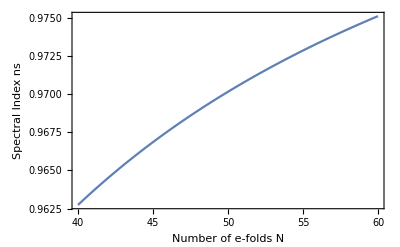

```mathematica
p1=Plot[1+3/(8 Y^2)-3/(2 Y),{Y,40,60},AxesLabel->{N,"ns"},PlotStyle->97,Frame-> True,FrameLabel->{"Number of e-folds  N", "Spectral Index ns"}]
```

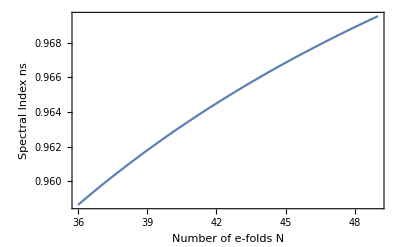

```mathematica
p3=Plot[0.9691,{Y,36,49},AxesLabel->{N,"ns"},PlotStyle->112,Frame-> True,FrameLabel->{"Number of e-folds  N", "Spectral Index ns"}];
p4=Plot[0.9607,{Y,36,49},AxesLabel->{N,"ns"},PlotStyle->112,Frame-> True,FrameLabel->{"Number of e-folds  N", "Spectral Index ns"}];
p2=Plot[1+3/(8 Y^2)-3/(2 Y),{Y,36,49},AxesLabel->{N,"ns"},PlotStyle->97,Frame-> True,FrameLabel->{"Number of e-folds  N", "Spectral Index ns"}]
```

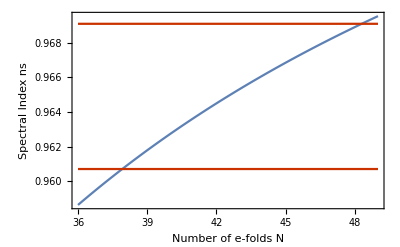

```mathematica
Show[p2,p3,p4]
```

```mathematica
Solve[ns==0.9691 ,Y]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Y→0.251301},{Y→48.2924}}

```mathematica
Solve[ns==0.9607,Y]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Y→0.251659},{Y→37.9163}}

So the e-foldings number has to be between 38 and 48 for the constraint on ns to be satisfied

```mathematica
About the tensor to scalar ratio, r:
```

```mathematica
Solve[r==0.056,Y]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Y→0.250881},{Y→71.1777}}

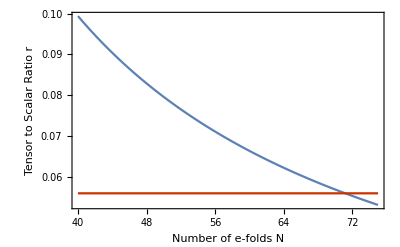

```mathematica
pr1=Plot[(-1+4 Y)/Y^2,{Y,40,75},PlotStyle->97,Frame-> True,FrameLabel->{"Number of e-folds  N", "Tensor to Scalar Ratio r"},PlotRange->Full];
pr2=Plot[0.056,{Y,40,75},PlotStyle->112,Frame-> True,FrameLabel->{"Number of e-folds  N", "Tensor to Scalar Ratio r"},PlotRange->Full];
Show[pr1,pr2]
```

For r to be smaller than 0.056, Y needs to be greater than 71, thus the constraints on ns and r cannot be satisfied simultaneously.

```mathematica
About the  slow-roll indices,ϵ1 and ϵ2, that are equal in this case:
```

```mathematica
ϵ1i
```

-1/(16 Y^2)+1/(4 Y)

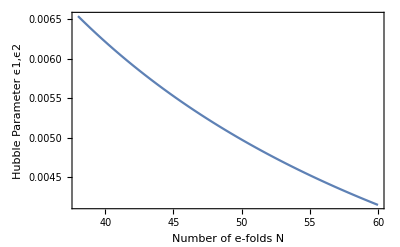

```mathematica
Plot[-1/(16 Y^2)+1/(4 Y),{Y,38,60},PlotStyle->97,Frame-> True,FrameLabel->{"Number of e-folds N", "Hubble Parameter ϵ1,ϵ2"},PlotRange->All]
```

```mathematica
About the potential slow-roll index,ϵ:
```

```mathematica
ϵi
```

-1/(16 Y^2 α)+1/(4 Y α)

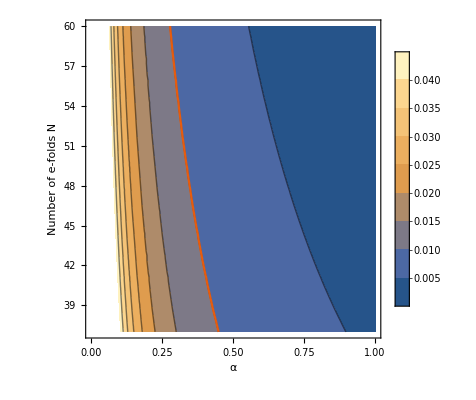

```mathematica
pe1=ContourPlot[-1/(36 Y^2 α)+1/(6 Y α),{α,0,1},{Y,37,60},PlotTheme->"Rainbow",PlotLegends->Automatic, FrameLabel->{α,"Number of e-folds N"}];
pe2=ContourPlot[-1/(36 Y^2 α)+1/(6 Y α)==0.01,{α,0,1},{Y,37,60},PlotTheme->"Scientific",PlotLegends->Automatic, FrameLabel->{α,"Number of e-folds N"}];
Show[pe1,pe2]
```